6

{{30,70,0,0,0,0,0,0,0,0,0,0},{9,21,31,38,0,0,0,0,0,0,0,0},{4,13,13,16,33,20,0,0,0,0,0,0},{3,7,11,10,11,20,25,13,0,0,0,0},{2,4,8,9,8,8,14,20,18,9,0,0},{2,2,5,8,7,6,7,10,15,18,14,7}}

{100,99,99,100,100,101}

0.0416191 (2-Cos[t]-Sin[t]+t Sin[t]^2+Sin[t]^6)

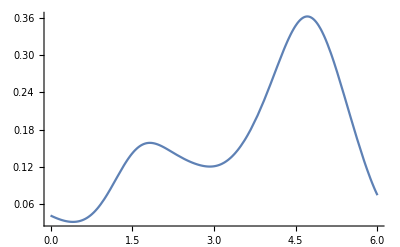

```mathematica
T=RandomInteger[{1,20}]
stake =100;
f[x_] = (x*Sin[x]^2+D[Cos[x],{x,T}]+D[Sin[x],{x,T}]+Sin[x]^T+2);
F[x_] = f[t]/NIntegrate[f[t],{t,0,T}];
S = Table[Table[Round[stake*NIntegrate[F[t],{t,i*T/rounds,(i+1)*T/rounds}]],{i,0,rounds-1}],{rounds,2,12,2}];
padS = Table[PadRight[Part[S,i],12],{i,1,6}]
check=Table[Sum[Part[padS,i,j],{j,1,Length[Part[S,i]]}],{i,1,6}]
F[x]
Plot[F[t],{t,0,T},PlotRange->Full ]
```